```mathematica
Which[
$HomeDirectory=="/Users/t.stohn",
SetDirectory["/Users/t.stohn/Desktop/Projects/MRA/scMRA-analysis"],
True,
Print["Are you on a different computer as usual?"]
];
```

## Model definition

```mathematica
TMAX=1000;
```

```mathematica
totalProteinContraints={
SosInactive-> SosTot- SosActive[t],
RasInactive->RasTot-RasActive[t],
Raf1Inactive-> Raf1Tot-Raf1Active[t],
MekInactive->MekTot-MekActive[t],
ErkInactive->ErkTot-ErkActive[t],
P90RskInactive->P90RskTot-P90RskActive[t],
PI3KInactive->PI3KTot- PI3KActive[t],
AktInactive->AktTot-AktActive[t],
C3GInactive->C3GTot-C3GActive[t],
Rap1Inactive->Rap1Tot-Rap1Active[t],
bRafInactive->bRafTot-bRafActive[t]
};

odes={
boundEGFReceptor'[t]==reaction0-reaction20,
freeEGFReceptor'[t]==reaction28-reaction29-reaction0,
SosActive'[t]==reaction1-reaction2-reaction13,
RasActive'[t]==reaction3-reaction4,
Raf1Active'[t]==reaction5-reaction6-reaction19,
MekActive'[t]==reaction7+reaction27-reaction8,
ErkActive'[t]==reaction9-reaction10,
P90RskActive'[t]==reaction11-reaction12,
PI3KActive'[t]==reaction14+reaction15-reaction16,
AktActive'[t]==reaction17-reaction18,
C3GActive'[t]==reaction21-reaction22,
Rap1Active'[t]==reaction23-reaction24,
bRafActive'[t]==reaction25-reaction26 +reaction30
};

vars={
boundEGFReceptor,
freeEGFReceptor,
SosActive,
RasActive,
Raf1Active,
MekActive,
ErkActive,
P90RskActive,
PI3KActive,
AktActive,
C3GActive,
Rap1Active,
bRafActive
};

rates ={
reaction0->(*$EGF+freeEGFReceptor->boundEGFReceptor;*)reaction0k1*EGF*freeEGFReceptor[t]-reaction0k2*boundEGFReceptor[t],
reaction1->(*SosInactive=>SosActive;*)reaction1Kcat*boundEGFReceptor[t]*SosInactive/(reaction1km+SosInactive),reaction2->(*SosActive=>SosInactive;*)reaction2k1*SosActive[t],
reaction3->(*RasInactive=>RasActive;*)reaction3Kcat*SosActive[t]*RasInactive/(reaction3km+RasInactive),reaction4->(*RasActive=>RasInactive;*)reaction4Kcat*RasGapActive*RasActive[t]/(reaction4km+RasActive[t]),
reaction5->(*Raf1Inactive=>Raf1Active;*)reaction5Kcat*RasActive[t]*Raf1Inactive/(reaction5km+Raf1Inactive),
reaction6->(*Raf1Active=>Raf1Inactive;*)reaction6Kcat*Raf1PPtase*Raf1Active[t]/(reaction6km+Raf1Active[t]),
reaction7->(*MekInactive=>MekActive;*)reaction7Kcat*Raf1Active[t]*MekInactive/(reaction7km+MekInactive),
reaction8->(*MekActive=>MekInactive;*)reaction8Kcat*PP2AActive*MekActive[t]/(reaction8km+MekActive[t]),
reaction9->(*ErkInactive=>ErkActive;*)reaction9Kcat*MekActive[t]*ErkInactive/(reaction9km+ErkInactive),
reaction10->(*ErkActive=>ErkInactive;*)reaction10Kcat*PP2AActive*ErkActive[t]/(reaction10km+ErkActive[t]),
reaction11->(*P90RskInactive=>P90RskActive;*)reaction11Kcat*ErkActive[t]*P90RskInactive/(reaction11km+P90RskInactive),
reaction12->(*P90RskActive=>P90RskInactive;*)reaction12k1*P90RskActive[t],
reaction13->(*SosActive=>SosInactive;*)reaction13Kcat*P90RskActive[t]*SosActive[t]/(reaction13km+SosActive[t]),
reaction14->(*PI3KInactive=>PI3KActive;*)reaction14Kcat*boundEGFReceptor[t]*PI3KInactive/(reaction14km+PI3KInactive),
reaction15->(*PI3KInactive=>PI3KActive;*)reaction15Kcat*RasActive[t]*PI3KInactive/(reaction15km+PI3KInactive),reaction16->(*PI3KActive=>PI3KInactive;*)reaction16k1*PI3KActive[t],
reaction17->(*AktInactive=>AktActive;*)reaction17Kcat*PI3KActive[t]*AktInactive/(reaction17km+AktInactive),
reaction18->(*AktActive=>AktInactive;*)reaction18k1*AktActive[t],
reaction19->(*Raf1Active=>Raf1Inactive;*)reaction19Kcat*AktActive[t]*Raf1Active[t]/(reaction19km+Raf1Active[t]),
reaction20->(*boundEGFReceptor=>degradedEGFReceptor;*)reaction20k1*boundEGFReceptor[t],
reaction21->(*C3GInactive=>C3GActive;*)reaction21kcat*boundEGFReceptor[t]*C3GInactive/(reaction21km+C3GInactive),
reaction22->(*C3GActive=>C3GInactive;*)reaction22k1*C3GActive[t],
reaction23->(*Rap1Inactive=>Rap1Active;*)reaction23kcat*C3GActive[t]*Rap1Inactive/(reaction23km+Rap1Inactive),
reaction24->(*Rap1Active=>Rap1Inactive;*)reaction24kcat*Rap1Gap*Rap1Active[t]/(reaction24km+Rap1Active[t]),
reaction25->(*bRafInactive=>bRafActive;*)reaction25kcat*Rap1Active[t]*bRafInactive/(reaction25km+bRafInactive),
reaction26->(*bRafActive=>bRafInactive;*)reaction26kcat*Raf1PPtase*bRafActive[t]/(reaction26km+bRafActive[t]),
reaction27->(*MekInactive=>MekActive;*)reaction27kcat*bRafActive[t]*MekInactive/(reaction27km+MekInactive),
reaction28->(*$proEGFReceptor=>freeEGFReceptor;*)reaction28v,
reaction29->(*freeEGFReceptor=>degradedEGFReceptor;*)reaction29k1*freeEGFReceptor[t],
reaction30->(*bRafInactive=>bRafActive;*)reaction30kcat*RasActive[t]*bRafInactive/(reaction30km+bRafInactive)
};

pars={
reaction0k1->0.000021, reaction0k2->0.121008,
reaction1Kcat->694.731,reaction1km->6086070,
reaction2k1->2.5,
reaction3Kcat->32.344,reaction3km->35954.3,
reaction4Kcat->1509.36,reaction4km->1432410,
reaction5Kcat->0.884096,reaction5km->62464.6,
reaction6Kcat->0.126329,reaction6km->1061.71,
reaction7Kcat->185.759,reaction7km->4768350,
reaction8Kcat->2.83243,reaction8km->518753,
reaction9Kcat->9.85367,reaction9km->1007340,
reaction10Kcat->8.8912,reaction10km->3496490,
reaction11Kcat->0.0213697,reaction11km->763523,
reaction12k1->0.005,
reaction13Kcat->1611.97,reaction13km->896896,
reaction14Kcat->10.6737,reaction14km->184912,
reaction15Kcat->0.0771067,reaction15km->272056,
reaction16k1->0.005,
(*reaction16k1->0.1,(*Increase inactivation of PI3K compared to original model to avoid very high PI3K/AKT*)*)
reaction17Kcat->0.0566279,reaction17km->653951,
reaction18k1->0.005,
reaction19Kcat->15.1212,reaction19km->119355,
reaction20k1->0.2,
reaction21kcat->694.731,reaction21km->6086070,reaction22k1->2.5,
reaction23kcat->32.344,reaction23km->35954.3,
reaction24kcat->1509.36,reaction24km->1432410,
reaction25kcat->0.884096,reaction25km->62464.6,
reaction26kcat->0.126329,reaction26km->1061.71,
reaction27kcat->185.759,reaction27km->4768350,
reaction28v->100,
reaction29k1->0.00125,
reaction30kcat->0.884096,reaction30km->62464.6,

SosTot-> 120000,
RasTot-> 120000,
Raf1Tot-> 120000,
MekTot->600000,
ErkTot->600000,
P90RskTot->120000,
PI3KTot->120000,
AktTot->120000,
C3GTot->120000,
Rap1Tot->120000,
bRafTot->120000,

EGF-> 10002000,
PP2AActive->120000,
Raf1PPtase->120000,
RasGapActive->120000,
Rap1Gap->120000,
proEGFReceptor->1
};

init={
(*EGF[0]==10002000,*)
boundEGFReceptor[0]==0,
freeEGFReceptor[0]==80000,
SosActive[0]==0,
RasActive[0]==0,
Raf1Active[0]==0,
MekActive[0]==0,
ErkActive[0]==0,
P90RskActive[0]==0,
PI3KActive[0]==0,
AktActive[0]==0,
C3GActive[0]==0,
Rap1Active[0]==0,
bRafActive[0]==0
};
```

```mathematica
totalProteins = totalProteinContraints⟦All,2,1⟧
```

{SosTot,RasTot,Raf1Tot,MekTot,ErkTot,P90RskTot,PI3KTot,AktTot,C3GTot,Rap1Tot,bRafTot}

```mathematica
sys={odes/.rates/.totalProteinContraints,  init, vars};
```

## Functions

### Time dynamics and Steady state solutions

```mathematica
ClearAll[appendT]
SetAttributes[appendT,Listable]
appendT[symbol_]:=ToExpression[ToString[symbol]<>"[t]"]
```

```mathematica
ClearAll[tsol]
tsol[sys_,pars_,tm_:TMAX]:=NDSolve[
Join[sys⟦1⟧,sys⟦2⟧]/.pars,sys⟦3⟧,
{t,0,tm}
]//Flatten
tsol::usage="tsol[system, parameters, tmax (optional)]: Time simulation of the whole system from (arbitratry) initial conditions. Only used to find estimation of steady state."
```

tsol[system, parameters, tmax (optional)]: Time simulation of the whole system from (arbitratry) initial conditions. Only used to find estimation of steady state.

```mathematica
xt[sys_,pars_, tval_]:=(appendT/@sys⟦3⟧)/.tsol[sys, pars,tval]/.t->tval
xt::usage="xt[sys, pars, t] gives the numerical value of the variables of the ODE system as vector";
```

```mathematica
ClearAll[ss]
ss[sys_,pars_,tm_:TMAX]:=Module[
{tmptsol=tsol[sys,pars, tm],
approx,
sscondition},
approx=Thread[{
sys⟦3⟧,
(sys⟦3⟧//appendT)/.t->TMAX/.tmptsol//Flatten
}];
sscondition=Thread[0==sys⟦1⟧⟦All,2⟧]/.pars/.x_[t]->x;
FindRoot[sscondition,approx]
]
ss::usage="ss[system, parameters, tmax]. Find steady state the of system. 
system = {{ODEs}, {Initial conditions}, {variables}}
Parameter = {p_i -> value,...}
tmax = Time to which dynamic simulation is run"
```

ss[system, parameters, tmax]. Find steady state the of system. 
system = {{ODEs}, {Initial conditions}, {variables}}
Parameter = {p_i -> value,...}
tmax = Time to which dynamic simulation is run

### Jacobian and local responses

```mathematica
ClearAll[rij]
rij[SYS_,PARS_,NODEi_,NODEj_,DELTA_:10^-6]:=Module[
{REFSS=ss[SYS,PARS],
dIN,dSS
},
dIN=DeleteCases[REFSS,NODEi->_]/.Rule[NODEj->ξ_, NODEj->(1+DELTA)ξ];
dSS=FindRoot[
(*Steady state condition*)
NODEi'[t]/.Flatten[ToRules/@SYS⟦1⟧]/.x_[t]->x/.PARS/.dIN,
{NODEi,NODEi/.REFSS}
];
(NODEj/NODEi/.REFSS)((NODEi/.dSS)-(NODEi/.REFSS))/((NODEj/.dIN)-(NODEj/.REFSS))
]
rij::usage="Calculate the local response coeffiecients of module MOD to a perturbation in node PERTURB at steady state REFSS;
Output: r_MOD_PERTURB → x_PERTRURB/x_MOD(∂SubscriptBox[x, MOD])/(∂SubscriptBox[x, PERTURB]); scaled value.";
```

```mathematica
ClearAll[si]
si[SYS_, PARS_,NODE_,DELTA_:10^-3]:=Module[{
REFSS=ss[SYS,PARS],
NODEtot=ToExpression[StringReplace[ToString[NODE], "Active"->"Tot"]],
dIN, dPARS,dSS
},
dPARS=PARS/.Rule[NODEtot->x_,NODEtot->(1+DELTA)x];
dIN=DeleteCases[REFSS,NODE->_];

dSS=FindRoot[
(*Steady state condition for NODE*)
NODE'[t]/.Flatten[ToRules/@SYS⟦1⟧]/.x_[t]->x/.dIN/.dPARS,
{NODE,NODE/.REFSS}];

NODEtot/(NODE/.REFSS)((NODE/.dSS)-(NODE/.REFSS))/(DELTA*NODEtot)

(*NODEtot/NODE* D[NODE'[t]/.Flatten[ToRules/@SYS⟦1⟧]/.x_[t]->x,NODEtot]/.REFSS/.PARS*)
]
si::usage="Calculate the sensitiity of node NODE to changes in the amount of total protein;
Output: s_NODE → NODE_TOT/NODE_Active(∂SubscriptBox[NODE, ACTIVE])/(∂SubscriptBox[NODE, TOT]); scaled value.";
```

### Perform perturbations

```mathematica
ClearAll[perturbPar]
SetAttributes[appendT,Listable]
perturbPar[pars_, perturb_, delta_]:=pars/.Flatten[Rule[#->val_, #-> (1+delta)*val]&/@Flatten[{perturb}]]
perturbPar::usage="perturbPar[pars, perturb, delta] changes the parameter perturb (1+delta)perturb.
perturb can be a signle parameter or a list of parameters."
```

perturbPar[pars, perturb, delta] changes the parameter perturb (1+delta)perturb.
perturb can be a signle parameter or a list of parameters.

```mathematica
maximumActive[sys_,pars_,tval_]:=(#-> FindMaxValue[{#[t]/.tsol[sys,pars],t>0,t<tval},{t,Min[4,tval]}])&/@sys⟦3⟧;
maximumActive::usage="maximumActive[sys,pars] returns the maximally active level of each node. Can be used to scale the tc-MRA equations"
```

maximumActive[sys,pars] returns the maximally active level of each node. Can be used to scale the tc-MRA equations

```mathematica
generateStochasticProteinAmounts[pars_,MU_,SIGMA_]:=pars/.(Rule[#->ξ_,#-> ξ*RandomReal[LogNormalDistribution[MU,SIGMA]]]&/@totalProteins);
generateStochasticProteinAmounts::usage="generateStochasticProteinAmounts[pars,μ,σ] returns pars with total protein abundances multiplied by a ramdon factor sampled LogNormalDistribution[μ,σ]"
```

generateStochasticProteinAmounts[pars,μ,σ] returns pars with total protein abundances multiplied by a ramdon factor sampled LogNormalDistribution[μ,σ]

```mathematica
ClearAll[pi]
pi[SYS_, PARS_,NODE_,PARTSOPERTURB_,DELTA_:0.1]:=Module[{
REFSS=ss[SYS,PARS],
dIN, dPARS,dSS
},
dPARS=perturbPar[PARS, PARTSOPERTURB,DELTA];
dIN=DeleteCases[REFSS,NODE->_];

dSS=FindRoot[
(*Steady state condition for NODE*)
NODE'[t]/.Flatten[ToRules/@SYS⟦1⟧]/.x_[t]->x/.dIN/.dPARS,
{NODE,NODE/.REFSS}];

((NODE/.dSS)-(NODE/.REFSS))/(NODE/.REFSS)

(*NODEtot/NODE* D[NODE'[t]/.Flatten[ToRules/@SYS⟦1⟧]/.x_[t]->x,NODEtot]/.REFSS/.PARS*)
]
si::usage="Calculate the sensitiity of node NODE to a direct perturbation;
Output: p_(NODE, PERTURBATION) → P_m/NODE_Active(∂SubscriptBox[NODE, ACTIVE])/(∂SubscriptBox[p, m])(∆SubscriptBox[p, m])/p_m; scaled value.";
```

## Perform the single-cell simulations

### Model exploration

```mathematica
ts = tsol[sys, pars, TMAX]//Flatten;
Plot[
Evaluate[#[t]&/@vars/.ts],
{t,0,30},
PlotRange->Full,
PlotLabels->(Style[Text[#], FontSize->10]&/@vars)
]
```

-Graphics-

Most of the dynamics occurs in the first 30/60 minutes, so we' ll focus on that timeframe. The accumulation of active Akt might be a typo in the Orton model (e.g. too low degradation rate?) but it is present in the original model, so we keep it.  

Note that the fraction of Active protein in steady state is very low for most proteins.

```mathematica
totalProteinContraints
```

{SosInactive→SosTot-SosActive[t],RasInactive→RasTot-RasActive[t],Raf1Inactive→Raf1Tot-Raf1Active[t],MekInactive→MekTot-MekActive[t],ErkInactive→ErkTot-ErkActive[t],P90RskInactive→P90RskTot-P90RskActive[t],PI3KInactive→PI3KTot-PI3KActive[t],AktInactive→AktTot-AktActive[t],C3GInactive→C3GTot-C3GActive[t],Rap1Inactive→Rap1Tot-Rap1Active[t],bRafInactive→bRafTot-bRafActive[t]}

```mathematica
{vars⟦3;;-1⟧,(ss[sys,pars]⟦3;;-1,2⟧)/(totalProteins/.pars)}//Thread
```

{{SosActive,0.00423507},{RasActive,0.000833448},{Raf1Active,0.000020473},{MekActive,0.00148953},{ErkActive,0.0178073},{P90RskActive,0.0494605},{PI3KActive,0.83957},{AktActive,0.619927},{C3GActive,0.0219074},{Rap1Active,0.00430908},{bRafActive,0.000214472}}

On the other hand, at the transient peak, most proteins are for a considerable part in their Active state

```mathematica
{vars⟦3;;-1⟧,(FindMaxValue[{#[t]/.ts,t>0,t<TMAX},{t,30}]&/@vars⟦3;;-1⟧)/(totalProteins/.pars)}//Thread//Quiet
```

{{SosActive,0.766824},{RasActive,0.146946},{Raf1Active,0.015083},{MekActive,0.541862},{ErkActive,0.919642},{P90RskActive,0.156557},{PI3KActive,0.99815},{AktActive,0.619925},{C3GActive,0.767109},{Rap1Active,0.147},{bRafActive,0.121531}}

### Calculate ground truth

```mathematica
rloc=Table[If[ToString[i]==ToString[j],-1,Chop[rij[sys,pars,i,j],10^-6]],{i,vars⟦3;;⟧},{j,vars⟦3;;⟧}];//Quiet
rloc//MatrixForm
```

(-1 | 0 | 0 | 0 | 0 | -0.807052 | 0 | 0 | 0 | 0 | 0
0.999877 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.00139 | -1 | 0 | 0 | 0 | 0 | -0.398718 | 0 | 0 | 0
0 | 0 | 0.0871739 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0.913221
0 | 0 | 0 | 0.991678 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.95669 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0.000176259 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.396081 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.99936 | -1 | 0
0 | 0.165986 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.858178 | -1)

```mathematica
rDS = Dataset[
AssociationThread[
StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],
AssociationThread[StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],#]&/@rloc
]
]
Export[
"results/orton-bmcsysbio-2009/rloc-true.tsv",
rDS]
```

results/orton-bmcsysbio-2009/rloc-true.tsv

```mathematica
sDS = Dataset[
AssociationThread[
StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],
AssociationThread[StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],#]&/@IdentityMatrix[Length[vars⟦3;;⟧]](si[sys, pars, #]&/@vars⟦3;;⟧)
]
]
Export[
"results/orton-bmcsysbio-2009/stot-true.tsv",
sDS]
```

results/orton-bmcsysbio-2009/stot-true.tsv

### Simulate 10000 cell population

```mathematica
pop=Table[generateStochasticProteinAmounts[pars, 0, .1],10000];
```

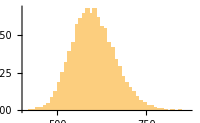

figures/simulations/distribution-ErkTot.pdf

```mathematica
plt = Histogram[
(ErkTot/.pop)/1000,
50,"Probability",
Frame->{1,1,0,0},
FrameLabel->(Style[#, FontFamily->"Helvetica", FontSize->8]&/@{"Erk^Tot", "Frequency"}),
PlotRange->Full,
ImageSize->200
]
Export["figures/simulations/distribution-ErkTot.pdf", plt]
```

Simulate the steady state of all 1000 cells.

There is a correlation between total and phospho ERK of 0.43

```mathematica
population=Join[#,ss[sys,#]]&/@pop;
```

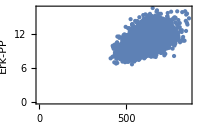

```mathematica
ListPlot[
Evaluate[{ErkTot/1000,ErkActive/1000}/.population],
Frame->{{True,False},{True,False}},
FrameLabel->(Style[#, FontFamily->"Helvetica", FontSize->8]&/@{"Erk^Tot", "Erk-PP"}),
PlotRange->All,
AxesOrigin->{0,0},
PlotStyle->PointSize[Small],
ImageSize->200

]
```

```mathematica
Correlation[Log[ErkTot]/.population,Log[ErkActive]/.population]
```

0.468087

But the correlation between Mek-PP and ERK-PP is much stronger

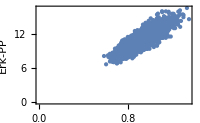

```mathematica
ListPlot[
Evaluate[{MekActive/1000,ErkActive/1000}/.population],
Frame->{{True,False},{True,False}},
FrameLabel->(Style[#, FontFamily->"Helvetica", FontSize->8]&/@{"Mek^PP", "Erk-PP"}),
PlotRange->All,
AxesOrigin->{0,0},
PlotStyle->PointSize[Small],
ImageSize->200

]
```

```mathematica
Correlation[Log[MekActive]/.population,Log[ErkActive]/.population]
```

0.845872

```mathematica
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.population),
Join[vars⟦3;;⟧,totalProteins]
]
];
(*Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1.tsv",df]*)
```

### Simulate populations with inhibitors

We model the inhibition of nodes   80% reduction in the kcat of the reaction X_inactive --> X_active. Note that some nodes are activated by multiple reactions, in which case all kcat of activating reactions are reduces by 80%. In addition we also model a weak perturbation of 25% reduction in catalytic activity.

#### Ras inhibition

Generate the parameters and check the mean log2 fold changes.

```mathematica
(*parsRasi=perturbPar[pars, reaction3Kcat, -.8];*)
parsRasi=perturbPar[pars, reaction3Kcat, -.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasi])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.0590068,RasActive→-0.355992,Raf1Active→-0.356423,MekActive→-0.077344,ErkActive→-0.0767176,P90RskActive→-0.0734791,PI3KActive→-0.0000556169,AktActive→-0.0000220291,C3GActive→0.,Rap1Active→0.,bRafActive→-0.0532912}

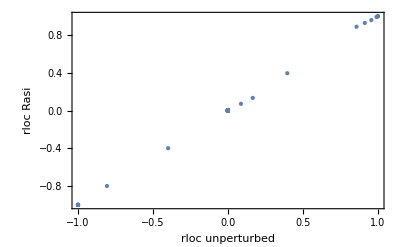

```mathematica
rlocRasi=Table[If[ToString[i]==ToString[j],-1,Chop[rij[sys,parsRasi,i,j],10^-6]],{i,vars⟦3;;⟧},{j,vars⟦3;;⟧}];//Quiet
ListPlot[
Thread[{Flatten[rloc], Flatten[rlocRasi]}],
PlotStyle->{PointSize[Large]},
Frame->True,
FrameLabel->{"rloc unperturbed", "rloc Rasi" }
]
```

```mathematica
popRasi=Table[generateStochasticProteinAmounts[parsRasi, 0, .1],2000];
populationRasi=Join[#,ss[sys,#]]&/@popRasi;
```

```mathematica
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasi),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASi-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASi-delta=0.25.tsv

#### p90RSK inhibition

Generate the parameters and check the mean log2 fold changes.

```mathematica
(*parsp90i =perturbPar[pars, reaction11Kcat, -.8];*)
parsp90i =perturbPar[pars, reaction11Kcat, -.25];
Thread[vars->Log2[(vars/.ss[sys, parsp90i])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.263724,RasActive→0.263688,Raf1Active→0.264083,MekActive→0.0675484,ErkActive→0.0669727,P90RskActive→-0.334626,PI3KActive→0.0000509853,AktActive→0.0000201941,C3GActive→0.,Rap1Active→0.,bRafActive→0.0472782}

```mathematica
popp90i=Table[generateStochasticProteinAmounts[parsp90i, 0, .1],2000];
populationp90i=Join[#,ss[sys,#]]&/@popp90i;
```

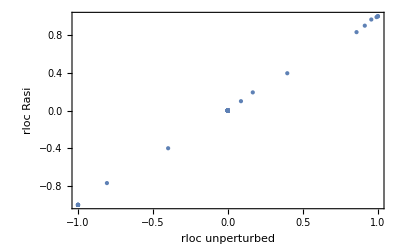

```mathematica
rlocp90i=Table[If[ToString[i]==ToString[j],-1,Chop[rij[sys,parsp90i,i,j],10^-6]],{i,vars⟦3;;⟧},{j,vars⟦3;;⟧}];//Quiet
ListPlot[
Thread[{Flatten[rloc], Flatten[rlocp90i]}],
PlotStyle->{PointSize[Large]},
Frame->True,
FrameLabel->{"rloc unperturbed", "rloc Rasi" }
]
```

```mathematica
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationp90i),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-p90i-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-p90i-delta=0.25.tsv

#### Sos inhibition

```mathematica
(*parsSosi =perturbPar[pars, reaction1Kcat, -.8];*)
parsSosi =perturbPar[pars, reaction1Kcat, -.25];
Thread[vars->Log2[(vars/.ss[sys, parsSosi])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→-0.35482,RasActive→-0.354781,Raf1Active→-0.355211,MekActive→-0.0771059,ErkActive→-0.0764813,P90RskActive→-0.0732526,PI3KActive→-0.00005545,AktActive→-0.000021963,C3GActive→0.,Rap1Active→0.,bRafActive→-0.0531285}

```mathematica
popSosi=Table[generateStochasticProteinAmounts[parsSosi, 0, .1],2000];
populationSosi=Join[#,ss[sys,#]]&/@popSosi;
```

```mathematica
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationSosi),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Sosi-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Sosi-delta=0.25.tsv

#### Raf1 inhibition

```mathematica
(*parsRaf1i =perturbPar[pars, reaction5Kcat, -.8];*)
parsRaf1i =perturbPar[pars, reaction5Kcat, -.25];
Thread[vars->Log2[(vars/.ss[sys, parsRaf1i])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.0207888,RasActive→0.0207862,Raf1Active→-0.394732,MekActive→-0.0271849,ErkActive→-0.0269608,P90RskActive→-0.0258037,PI3KActive→3.69022×10^-6,AktActive→1.46163×10^-6,C3GActive→-4.80514×10^-16,Rap1Active→-6.40685×10^-16,bRafActive→0.00347122}

```mathematica
popRaf1i=Table[generateStochasticProteinAmounts[parsRaf1i, 0, .1],2000];
populationRaf1i=Join[#,ss[sys,#]]&/@popRaf1i;
```

```mathematica
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRaf1i),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Raf1i-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Raf1i-delta=0.25.tsv

#### Mek inhibition

Mek is activated by both Raf1 (reaction 7) and bRaf (reaction 27), so we need to reduce both kcats.

```mathematica
(*parsMeki =perturbPar[pars, {reaction7Kcat, reaction27kcat}, -0.8];*)
parsMeki =perturbPar[pars, {reaction7Kcat, reaction27kcat}, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsMeki])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.261876,RasActive→0.261841,Raf1Active→0.262232,MekActive→-0.348144,ErkActive→-0.345575,P90RskActive→-0.332222,PI3KActive→0.0000505948,AktActive→0.0000200394,C3GActive→0.,Rap1Active→0.,bRafActive→0.0469215}

```mathematica
popMeki=Table[generateStochasticProteinAmounts[parsMeki, 0, .1],2000];
populationMeki=Join[#,ss[sys,#]]&/@popMeki;

df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationMeki),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Meki-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Meki-delta=0.25.tsv

#### Erk Inhibition

```mathematica
(*parsErki =perturbPar[pars, reaction9Kcat, -0.8];*)
parsErki =perturbPar[pars, reaction9Kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsErki])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.261784,RasActive→0.261749,Raf1Active→0.262141,MekActive→0.0670174,ErkActive→-0.345452,P90RskActive→-0.332103,PI3KActive→0.0000505755,AktActive→0.0000200318,C3GActive→0.,Rap1Active→-3.20343×10^-16,bRafActive→0.0469038}

```mathematica
popErki=Table[generateStochasticProteinAmounts[parsErki, 0, .1],2000];
populationErki=Join[#,ss[sys,#]]&/@popErki;

df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationErki),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Erki-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Erki-delta=0.25.tsv

#### p90Rsk inhibition

```mathematica
(*parsp90Rski =perturbPar[pars, reaction11Kcat, -0.8];*)
parsp90Rski =perturbPar[pars, reaction11Kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsp90Rski])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.263724,RasActive→0.263688,Raf1Active→0.264083,MekActive→0.0675484,ErkActive→0.0669727,P90RskActive→-0.334626,PI3KActive→0.0000509853,AktActive→0.0000201941,C3GActive→0.,Rap1Active→0.,bRafActive→0.0472782}

```mathematica
popp90Rski=Table[generateStochasticProteinAmounts[parsp90Rski, 0, .1],2000];
populationp90Rski=Join[#,ss[sys,#]]&/@popp90Rski;

df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationp90Rski),
Join[vars⟦3;;⟧,totalProteins]
]
];
(*Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-p90Rski.tsv",df]*)
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-p90Rski-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-p90Rski-delta=0.25.tsv

#### PI3K inhibition

PI3K is activate by EGFR (reaction 13) and RAS (reaction 14), so the kcat of both needs to be reduced

```mathematica
(*parsPI3K =perturbPar[pars, {reaction13Kcat, reaction14Kcat}, -0.8];*)
parsPI3K =perturbPar[pars, {reaction13Kcat, reaction14Kcat}, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsPI3K])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.27341,RasActive→0.273373,Raf1Active→0.287068,MekActive→0.0715479,ErkActive→0.0709371,P90RskActive→0.0677905,PI3KActive→-0.0830313,AktActive→-0.0335096,C3GActive→0.,Rap1Active→-3.20343×10^-16,bRafActive→0.0491541}

```mathematica
popPI3K=Table[generateStochasticProteinAmounts[parsPI3K, 0, .1],2000];
populationPI3K=Join[#,ss[sys,#]]&/@popPI3K;

df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationPI3K),
Join[vars⟦3;;⟧,totalProteins]
]
];
(*Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-PI3Ki.tsv",df]*)
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-PI3Ki-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-PI3Ki-delta=0.25.tsv

#### AKT inhibition

```mathematica
(*parsAkti =perturbPar[pars, reaction17Kcat, -0.8];*)
parsAkti =perturbPar[pars, reaction17Kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsAkti])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→-1.60171×10^-16,freeEGFReceptor→-3.20343×10^-16,SosActive→-0.00398262,RasActive→-0.00398214,Raf1Active→0.065181,MekActive→0.00520024,ErkActive→0.00515688,P90RskActive→0.00493315,PI3KActive→-7.0092×10^-7,AktActive→-0.180171,C3GActive→-4.80514×10^-16,Rap1Active→-6.40685×10^-16,bRafActive→-0.000660211}

```mathematica
popAkti=Table[generateStochasticProteinAmounts[parsAkti, 0, .1],2000];
populationAkti=Join[#,ss[sys,#]]&/@popAkti;

df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationAkti),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Akti.tsv",df]
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Akti-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Akti.tsv

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Akti-delta=0.25.tsv

#### C3G inhibition

```mathematica
(*parsC3Gi =perturbPar[pars, reaction21kcat, -0.8];*)
parsC3Gi =perturbPar[pars, reaction21kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsC3Gi])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.188388,RasActive→0.188364,Raf1Active→0.188638,MekActive→-0.249089,ErkActive→-0.247188,P90RskActive→-0.237325,PI3KActive→0.0000354606,AktActive→0.0000140452,C3GActive→-0.407262,Rap1Active→-0.407036,bRafActive→-0.298648}

```mathematica
popC3Gi=Table[generateStochasticProteinAmounts[parsC3Gi, 0, .1],2000];
populationC3Gi=Join[#,ss[sys,#]]&/@popC3Gi;

df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationC3Gi),
Join[vars⟦3;;⟧,totalProteins]
]
];
(*Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-C3Gi.tsv",df]*)
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-C3Gi-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-C3Gi-delta=0.25.tsv

#### Rap1 inhibition

```mathematica
(*parsRap1i =perturbPar[pars, reaction23kcat, -0.8];*)
parsRap1i =perturbPar[pars, reaction23kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsRap1i])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→-1.60171×10^-16,freeEGFReceptor→-3.20343×10^-16,SosActive→0.191638,RasActive→0.191613,Raf1Active→0.191892,MekActive→-0.253445,ErkActive→-0.251513,P90RskActive→-0.241492,PI3KActive→0.0000361137,AktActive→0.0000143038,C3GActive→-4.80514×10^-16,Rap1Active→-0.414807,bRafActive→-0.304023}

```mathematica
popRap1i=Table[generateStochasticProteinAmounts[parsRap1i, 0, .1],2000];
populationRap1i=Join[#,ss[sys,#]]&/@popRap1i;

df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRap1i),
Join[vars⟦3;;⟧,totalProteins]
]
];
(*Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Rap1i.tsv",df]*)
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Rap1i-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-Rap1i-delta=0.25.tsv

#### bRaf inhibition

```mathematica
(*parsbRafi =perturbPar[pars, {reaction25kcat, reaction30kcat}, -0.8];*)
parsbRafi =perturbPar[pars, {reaction25kcat, reaction30kcat}, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsbRafi])/(vars/.ss[sys, pars])]]
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.237977,RasActive→0.237945,Raf1Active→0.238298,MekActive→-0.3158,ErkActive→-0.313444,P90RskActive→-0.301205,PI3KActive→0.0000455884,AktActive→0.0000180565,C3GActive→-4.80514×10^-16,Rap1Active→-6.40685×10^-16,bRafActive→-0.381643}

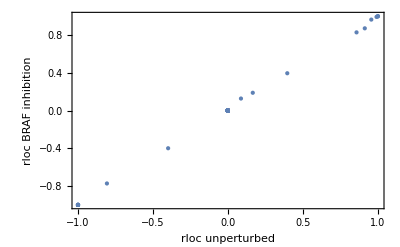

```mathematica
rlocbRafi=Table[If[ToString[i]==ToString[j],-1,Chop[rij[sys,parsbRafi,i,j],10^-6]],{i,vars⟦3;;⟧},{j,vars⟦3;;⟧}];//Quiet
ListPlot[
Thread[{Flatten[rloc], Flatten[rlocbRafi]}],
PlotStyle->{PointSize[Large]},
Frame->True,
FrameLabel->{"rloc unperturbed", "rloc BRAF inhibition" }
]
```

```mathematica
popbRafi=Table[generateStochasticProteinAmounts[parsbRafi, 0, .1],2000];
populationbRafi=Join[#,ss[sys,#]]&/@popbRafi;

df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationbRafi),
Join[vars⟦3;;⟧,totalProteins]
]
];
(*Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-bRafi.tsv",df]*)
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-bRafi-delta=0.25.tsv",df]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-bRafi-delta=0.25.tsv

#### Exploration of the effect of node inhibitions

In reconstructions we have found that sometimes including a limited number of perturbations decreases reconstruction performance. Importantly, when using a “full perturbation” design, this is not the case. Here, we will explore why that might be the case.

A first hypothesis is that the true local response coefficients differ (strongly) between the reference steady state (that we try to reconstruct), and the steady state of the perturbed network. The plot below suggests that the relation between p90RSK and SOS (p90RSK is a feedback inhibitor of SOS) is much stronger around the MEKi (green) steady state that around the RASi steady state (orange).

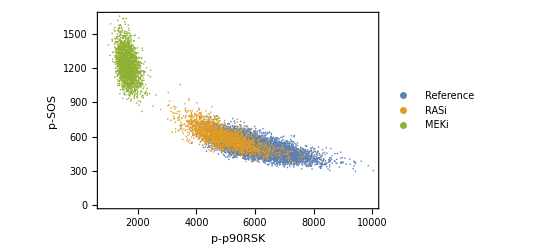

```mathematica
ListPlot[
{{P90RskActive, SosActive}/.population,
{P90RskActive, SosActive}/.populationRasi,
{P90RskActive, SosActive}/.populationMeki
},
PlotRange->Full,
Frame->True,
FrameLabel->{"p-p90RSK","p-SOS"},
PlotLegends->{"Reference","RASi", "MEKi"}
]
```

However, when we consider the local response coefficients that we want to reconstruct, they are actually fairly similar.

```mathematica
rlocRasi=Table[If[ToString[i]==ToString[j],-1,Chop[rij[sys,parsRasi,i,j],10^-6]],{i,vars⟦3;;⟧},{j,vars⟦3;;⟧}];//Quiet
rlocMeki=Table[If[ToString[i]==ToString[j],-1,Chop[rij[sys,parsMeki,i,j],10^-6]],{i,vars⟦3;;⟧},{j,vars⟦3;;⟧}];//Quiet
```

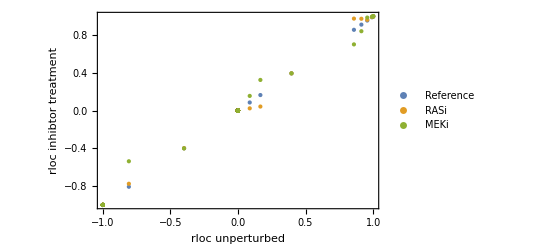

```mathematica
ListPlot[
{
Thread[{Flatten[rloc], Flatten[rloc]}],
Thread[{Flatten[rloc], Flatten[rlocRasi]}],
Thread[{Flatten[rloc], Flatten[rlocMeki]}]},
PlotStyle->{PointSize[Medium]},
Frame->True,
FrameLabel->{"rloc unperturbed", "rloc inhibtor treatment" },
PlotLegends->{"Reference","RASi", "MEKi"}
]
```

Although the Rasi rloc values are considerable more similar.

```mathematica
Power[Thread[{Flatten[rloc]- Flatten[rlocRasi]}]//Flatten,2]//Total
Power[Thread[{Flatten[rloc]- Flatten[rlocMeki]}]//Flatten,2]//Total
```

0.0378533

0.133531

The interpretation of the rloc values is the partial logarithmic derivative, and this looks much more linear.

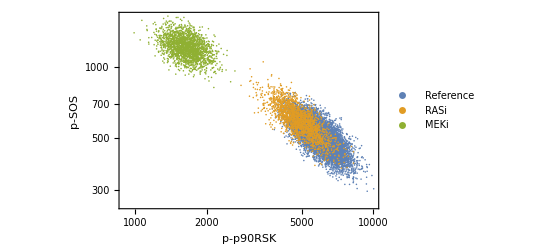

```mathematica
ListLogLogPlot[
{{P90RskActive, SosActive}/.population,
{P90RskActive, SosActive}/.populationRasi,
{P90RskActive, SosActive}/.populationMeki
},
PlotRange->Full,
Frame->True,
FrameLabel->{"p-p90RSK","p-SOS"},
PlotLegends->{"Reference","RASi", "MEKi"}
]
```

Let’s check how well our formalism models the data (in the absence of noise). We use the true local response coefficients to “predict” the effect of total protein variations on the protein activities. The plot below shows that for the reference state, this gives an excellent agreement.

```mathematica
sMatrix:=DiagonalMatrix[si[sys, pars, #]&/@vars⟦3;;⟧]
```

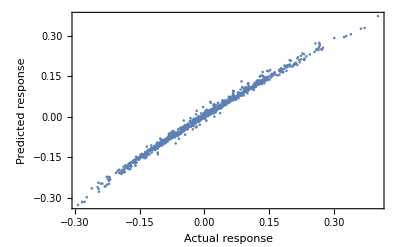

```mathematica
tmp = population⟦1;;100⟧;
refActive = Mean[vars⟦3;;⟧/.tmp];
refTotal =Mean[totalProteins/.tmp];

rGlobTot=Transpose[(totalProteins-refTotal)/refTotal/.tmp];
rGlob=Transpose[(vars⟦3;;⟧-refActive)/refActive/.tmp];
ListPlot[Thread[
{Flatten[rGlob],
-Flatten[Inverse[rloc].sMatrix.rGlobTot]}
],
Frame->True,
FrameLabel->{"Actual response", "Predicted response"}
]
```

However, if we look at a strong perturbations (80% reduction in catalytic activity of MEKi), we start seeing deviations for the points that have the strongest (negative) response.

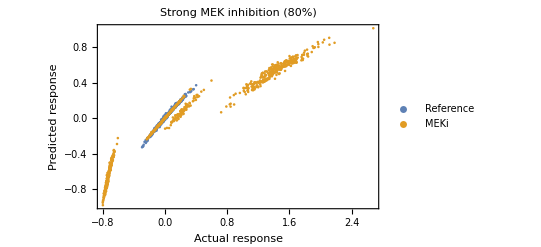

```mathematica
d=-0.8;
parsMekiLow=perturbPar[pars, {reaction7Kcat, reaction27kcat}, d];
popMekiLow=Table[generateStochasticProteinAmounts[parsMekiLow, 0, 0.1],100];

populationMekiLow=Join[#,ss[sys,#]]&/@popMekiLow;

rGlobTotMeki=Transpose[(totalProteins-refTotal)/refTotal/.populationMekiLow];
rGlobMeki=Transpose[(vars⟦3;;⟧-refActive)/refActive/.populationMekiLow];
tmp=pi[sys,pars,#,{reaction7Kcat, reaction27kcat},d]&/@vars⟦3;;⟧//Quiet//Chop;
piMeki=Transpose[Table[tmp,Length[populationMekiLow]]]//Quiet;
rlocinv=Inverse[rloc];
predictMeki=-rlocinv.(sMatrix.rGlobTotMeki+piMeki);
ListPlot[
{Thread[
{Flatten[rGlob],
-Flatten[Inverse[rloc].sMatrix.rGlobTot]}],
Thread[{
Flatten[rGlobMeki],
Flatten[predictMeki]}]
},
PlotRange->Full,
(*PlotStyle->{PointSize->Small},*)
Frame->True,
FrameLabel->{"Actual response", "Predicted response"},
PlotLabel->"Strong MEK inhibition (80%)",
PlotLegends->{"Reference","MEKi"}
]
```

```mathematica
PairedHistogram[
Flatten[rloc.rGlob+sMatrix.rGlobTot],
Flatten[rloc.rGlobMeki+sMatrix.rGlobTotMeki + piMeki],
ChartLabels->{"No perturbation", "Strong MEK inhibition (80%)"},
PlotLabel->"Distribution of Residuals",
PlotTheme->"Business",
BarSpacing->None
]
```

However, our method does not directly minimize the difference between actual and predicted response, but minimizes the residuals of the MRA equations . We can also check how those distributions look, and these are indeed much broader for (a subset of) the MRA equations .

-Graphics-

For weak perturbations this does not seem to be the case.

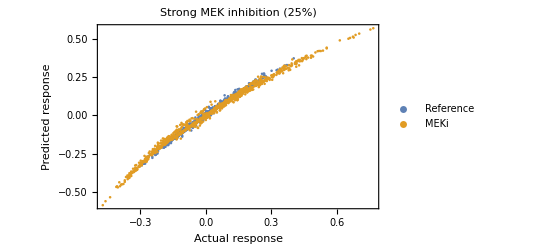

```mathematica
d=-0.25;
parsMekiLow=perturbPar[pars, {reaction7Kcat, reaction27kcat}, d];
popMekiLow=Table[generateStochasticProteinAmounts[parsMekiLow, 0, 0.1],100];

populationMekiLow=Join[#,ss[sys,#]]&/@popMekiLow;

rGlobTotMeki=Transpose[(totalProteins-refTotal)/refTotal/.populationMekiLow];
rGlobMeki=Transpose[(vars⟦3;;⟧-refActive)/refActive/.populationMekiLow];
tmp=pi[sys,pars,#,{reaction7Kcat, reaction27kcat},d]&/@vars⟦3;;⟧//Quiet//Chop;
piMeki=Transpose[Table[tmp,Length[populationMekiLow]]]//Quiet;
rlocinv=Inverse[rloc];
predictMeki=-rlocinv.(sMatrix.rGlobTotMeki+piMeki);
ListPlot[
{Thread[
{Flatten[rGlob],
-Flatten[Inverse[rloc].sMatrix.rGlobTot]}],
Thread[{
Flatten[rGlobMeki],
Flatten[predictMeki]}]
},
PlotRange->Full,
(*PlotStyle->{PointSize->Small},*)
Frame->True,
FrameLabel->{"Actual response", "Predicted response"},
PlotLabel->"Strong MEK inhibition (25%)",
PlotLegends->{"Reference","MEKi"}
]
```

```mathematica
PairedHistogram[
Flatten[rloc.rGlob+sMatrix.rGlobTot],
Flatten[rloc.rGlobMeki+sMatrix.rGlobTotMeki + piMeki],
ChartLabels->{"No perturbation", "Strong MEK inhibition (80%)"},
PlotLabel->"Distribution of Residuals",
PlotTheme->"Business",
BarSpacing->None
]
```

-Graphics-

### Simulate BRAF mutation cells

We model a BRAF mutation by a 100-fold reduction in the BRAF deactivation rate.

```mathematica
parsBRAF=pars/.Rule[reaction26kcat->x_,reaction26kcat->0.01*x];
```

This indeed leads to high Erk and Mek activation

```mathematica
tsBRAF=tsol[sys,parsBRAF];
Plot[
Evaluate[#[t]&/@vars/.tsBRAF],
{t,0,10},
PlotRange->Full,
PlotLabels->(Style[Text[#], FontSize->10]&/@vars)
]
```

-Graphics-

And a roughly 75% steady state activation rate of BRAF, compared to a very low one in the non-mutant model.

```mathematica
(bRafActive/.ss[sys,parsBRAF])/(bRafTot/.parsBRAF)
(bRafActive/.ss[sys,pars])/(bRafTot/.pars)
```

0.751924

0.000214472

#### The ground truth values

```mathematica
rlocBRAF=Table[If[ToString[i]==ToString[j],-1,Chop[rij[sys,parsBRAF,i,j],10^-6]],{i,vars⟦3;;⟧},{j,vars⟦3;;⟧}];//Quiet
rDSBRAF = Dataset[
AssociationThread[
StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],
AssociationThread[StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],#]&/@rlocBRAF
]
]
Export[
"results/orton-bmcsysbio-2009/rloc-braf-true.tsv",
rDSBRAF]
```

results/orton-bmcsysbio-2009/rloc-braf-true.tsv

```mathematica
r
```

r

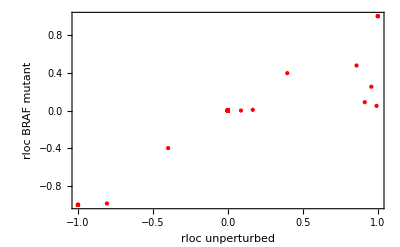

```mathematica
ListPlot[
Thread[{Flatten[rloc], Flatten[rlocBRAF]}],
PlotStyle->Directive[PointSize[Large],Red],
Frame->True,
FrameLabel->{"rloc unperturbed", "rloc BRAF mutant" }
]
```

```mathematica
sBRAFDS = Dataset[
AssociationThread[
StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],
AssociationThread[StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],#]&/@IdentityMatrix[Length[vars⟦3;;⟧]](si[sys, parsBRAF, #]&/@vars⟦3;;⟧)
]
]
Export[
"results/orton-bmcsysbio-2009/stot-braf-true.tsv",
sBRAFDS]
```

results/orton-bmcsysbio-2009/stot-braf-true.tsv

#### Simulate the BRAF mutant population

```mathematica
popBRAF=Table[generateStochasticProteinAmounts[parsBRAF, 0, .1],10000];
```

```mathematica
populationBRAF=Join[#,ss[sys,#]]&/@popBRAF//Quiet;
```

```mathematica
dfBRAF=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAF),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut.tsv",dfBRAF]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut.tsv

#### Simulate the BRAF mutant population with Inhibitors

p90 Inhibition

```mathematica
parsBRAFp90i =perturbPar[parsBRAF, reaction11Kcat, -.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFp90i])/(vars/.ss[sys, parsBRAF])]]

popBRAFp90i=Table[generateStochasticProteinAmounts[parsBRAFp90i, 0, .1],2000];
populationBRAFp90i=Join[#,ss[sys,#]]&/@popBRAFp90i;
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFp90i),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-p90i.tsv",df];
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.115311,RasActive→0.11531,Raf1Active→0.115323,MekActive→0.0000781379,ErkActive→3.85997×10^-6,P90RskActive→-0.117191,PI3KActive→1.69451×10^-6,AktActive→6.71235×10^-7,C3GActive→0.,Rap1Active→3.20343×10^-16,bRafActive→0.000883458}

RAS Inhibition

```mathematica
parsBRAFRasi=perturbPar[parsBRAF, reaction3Kcat, -.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFRasi])/(vars/.ss[sys, parsBRAF])]]

popBRAFRasi=Table[generateStochasticProteinAmounts[parsBRAFRasi, 0, .1],2000];
populationBRAFRasi=Join[#,ss[sys,#]]&/@popBRAFRasi;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFRasi),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-Rasi.tsv",df];
```

{boundEGFReceptor→-1.60171×10^-16,freeEGFReceptor→-3.20343×10^-16,SosActive→2.90868×10^-6,RasActive→-0.415031,Raf1Active→-0.41507,MekActive→-0.000237105,ErkActive→-0.0000117142,P90RskActive→-2.95419×10^-6,PI3KActive→-5.09127×10^-6,AktActive→-2.01677×10^-6,C3GActive→-4.80514×10^-16,Rap1Active→-3.20343×10^-16,bRafActive→-0.00267744}

Sos inhibition

```mathematica
parsBRAFSosi =perturbPar[parsBRAF, reaction1Kcat, -.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFSosi])/(vars/.ss[sys, parsBRAF])]]
popBRAFSosi=Table[generateStochasticProteinAmounts[parsBRAFSosi, 0, .1],2000];
populationBRAFSosi=Join[#,ss[sys,#]]&/@popBRAFSosi;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFSosi),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-Sosi.tsv",df];
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→-0.414931,RasActive→-0.414927,Raf1Active→-0.414967,MekActive→-0.000237054,ErkActive→-0.0000117116,P90RskActive→-2.95355×10^-6,PI3KActive→-5.09017×10^-6,AktActive→-2.01634×10^-6,C3GActive→0.,Rap1Active→3.20343×10^-16,bRafActive→-0.00267686}

Raf1 inhibition

```mathematica
parsBRAFRaf1i =perturbPar[parsBRAF, reaction5Kcat, -.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFRaf1i])/(vars/.ss[sys, parsBRAF])]]
popBRAFRaf1i=Table[generateStochasticProteinAmounts[parsBRAFRaf1i, 0, .1],2000];
populationBRAFRaf1i=Join[#,ss[sys,#]]&/@popBRAFRaf1i;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFRaf1i),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-Raf1i.tsv",df];
```

{boundEGFReceptor→-1.60171×10^-16,freeEGFReceptor→-3.20343×10^-16,SosActive→8.50647×10^-10,RasActive→8.50639×10^-10,Raf1Active→-0.415078,MekActive→-6.93478×10^-8,ErkActive→-3.42584×10^-9,P90RskActive→-8.63959×10^-10,PI3KActive→1.18527×10^-14,AktActive→4.80514×10^-15,C3GActive→-4.80514×10^-16,Rap1Active→-3.20343×10^-16,bRafActive→6.27359×10^-12}

Mek inhibition

Mek is activated by both Raf1 (reaction 7) and bRaf (reaction 27),so we need to reduce both kcats.

```mathematica
parsBRAFMeki =perturbPar[parsBRAF, {reaction7Kcat, reaction27kcat}, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFMeki])/(vars/.ss[sys, parsBRAF])]]
popBRAFMeki=Table[generateStochasticProteinAmounts[parsBRAFMeki, 0, .1],2000];
populationBRAFMeki=Join[#,ss[sys,#]]&/@popBRAFMeki;
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFMeki),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-Meki.tsv",df];
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.000531447,RasActive→0.000531442,Raf1Active→0.0005315,MekActive→-0.042653,ErkActive→-0.00213907,P90RskActive→-0.000539765,PI3KActive→7.50315×10^-9,AktActive→2.97217×10^-9,C3GActive→0.,Rap1Active→0.,bRafActive→3.92026×10^-6}

Erk inhibition

```mathematica
parsBRAFErki =perturbPar[parsBRAF, reaction9Kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFErki])/(vars/.ss[sys, parsBRAF])]]
popBRAFErki=Table[generateStochasticProteinAmounts[parsBRAFErki, 0, .1],2000];
populationBRAFErki=Join[#,ss[sys,#]]&/@popBRAFErki;
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFErki),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-Erki.tsv",df];
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.0776387,RasActive→0.0776379,Raf1Active→0.0776466,MekActive→0.0000519629,ErkActive→-0.289073,P90RskActive→-0.0788874,PI3KActive→1.12595×10^-6,AktActive→4.46014×10^-7,C3GActive→-4.80514×10^-16,Rap1Active→-3.20343×10^-16,bRafActive→0.000587452}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

p90 inhibition

```mathematica
parsBRAFp90Rski =perturbPar[parsBRAF, reaction11Kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFp90Rski])/(vars/.ss[sys, parsBRAF])]]
popBRAFp90Rski=Table[generateStochasticProteinAmounts[parsBRAFp90Rski, 0, .1],2000];
populationBRAFp90Rski=Join[#,ss[sys,#]]&/@popBRAFp90Rski;
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFp90Rski),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-p90Rski.tsv",df];
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→1.01401,RasActive→1.01399,Raf1Active→1.01415,MekActive→0.000931523,ErkActive→0.0000460029,P90RskActive→-1.03721,PI3KActive→0.0000207602,AktActive→8.22355×10^-6,C3GActive→0.,Rap1Active→3.20343×10^-16,bRafActive→0.0105681}

PI3K inhibition

```mathematica
parsBRAFPI3Ki =perturbPar[parsBRAF, {reaction13Kcat, reaction14Kcat}, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFPI3Ki])/(vars/.ss[sys, parsBRAF])]]
popBRAFPI3Ki=Table[generateStochasticProteinAmounts[parsBRAFPI3Ki, 0, .1],2000];
populationBRAFPI3Ki=Join[#,ss[sys,#]]&/@popBRAFPI3Ki;
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFPI3Ki),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-PI3Ki.tsv",df];
```

{boundEGFReceptor→-1.60171×10^-16,freeEGFReceptor→-3.20343×10^-16,SosActive→2.2356,RasActive→2.23555,Raf1Active→2.38594,MekActive→0.00314541,ErkActive→0.000155214,P90RskActive→0.0000391415,PI3KActive→-0.862877,AktActive→-0.410772,C3GActive→-4.80514×10^-16,Rap1Active→-3.20343×10^-16,bRafActive→0.0360034}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Akt inhibition

```mathematica
parsBRAFAkti =perturbPar[parsBRAF, reaction17Kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFAkti])/(vars/.ss[sys, parsBRAF])]]
popBRAFAkti=Table[generateStochasticProteinAmounts[parsBRAFAkti, 0, .1],2000];
populationBRAFAkti=Join[#,ss[sys,#]]&/@popBRAFAkti;
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFAkti),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-Akti.tsv",df];
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→-1.11848×10^-9,RasActive→-1.11847×10^-9,Raf1Active→0.410062,MekActive→9.11827×10^-8,ErkActive→4.5045×10^-9,P90RskActive→1.13599×10^-9,PI3KActive→-1.5857×10^-14,AktActive→-1.40391,C3GActive→-4.80514×10^-16,Rap1Active→0.,bRafActive→-8.24946×10^-12}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

C3G inhibition

```mathematica
parsBRAFC3Gi =perturbPar[parsBRAF, reaction21kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFC3Gi])/(vars/.ss[sys, parsBRAF])]]
popBRAFC3Gi=Table[generateStochasticProteinAmounts[parsBRAFC3Gi, 0, .1],2000];
populationBRAFC3Gi=Join[#,ss[sys,#]]&/@popBRAFC3Gi;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFC3Gi),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-C3Gi.tsv",df];
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.419712,RasActive→0.419708,Raf1Active→0.419761,MekActive→-4.34189,ErkActive→-1.22528,P90RskActive→-0.427356,PI3KActive→6.87615×10^-6,AktActive→2.7238×10^-6,C3GActive→-2.2969,Rap1Active→-2.29617,bRafActive→-6.73522}

Rap1 inhibition

```mathematica
parsBRAFRap1i =perturbPar[parsBRAF, reaction23kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFRap1i])/(vars/.ss[sys, parsBRAF])]]
popBRAFRap1i=Table[generateStochasticProteinAmounts[parsBRAFRap1i, 0, .1],2000];
populationBRAFRap1i=Join[#,ss[sys,#]]&/@popBRAFRap1i;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFRap1i),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-Rap1i.tsv",df];
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.431784,RasActive→0.431779,Raf1Active→0.431834,MekActive→-4.38052,ErkActive→-1.25221,P90RskActive→-0.439682,PI3KActive→7.10503×10^-6,AktActive→2.81446×10^-6,C3GActive→-4.80514×10^-16,Rap1Active→-2.32119,bRafActive→-6.77359}

Braf inhibition

```mathematica
parsBRAFbRafi =perturbPar[parsBRAF, {reaction25kcat, reaction30kcat}, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsBRAFbRafi])/(vars/.ss[sys, parsBRAF])]]
popBRAFbRafi=Table[generateStochasticProteinAmounts[parsBRAFbRafi, 0, .1],2000];
populationBRAFbRafi=Join[#,ss[sys,#]]&/@popBRAFbRafi;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationBRAFbRafi),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-BRAFmut-bRafi.tsv",df];
```

{boundEGFReceptor→-1.60171×10^-16,freeEGFReceptor→-3.20343×10^-16,SosActive→0.496815,RasActive→0.496809,Raf1Active→0.496874,MekActive→-4.57552,ErkActive→-1.39264,P90RskActive→-0.506126,PI3KActive→8.37152×10^-6,AktActive→3.31615×10^-6,C3GActive→-4.80514×10^-16,Rap1Active→-3.20343×10^-16,bRafActive→-6.96729}

### Simulate RAS mutation cells

We model a RAS mutation like before for BRAF by a 100-fold reduction in the RAS deactivation rate.

```mathematica
parsRAS=pars/.Rule[reaction4Kcat->x_,reaction4Kcat->0.01*x];
```

```mathematica
tsRAS=tsol[sys,parsRAS];
Plot[
Evaluate[#[t]&/@vars/.tsRAS],
{t,0,15},
PlotRange->Full,
PlotLabels->(Style[Text[#], FontSize->10]&/@vars)
]
```

-Graphics-

And a roughly 75% steady state activation rate of BRAF, compared to a very low one in the non-mutant model.

```mathematica
(RasActive/.ss[sys,parsRAS])/(RasTot/.parsRAS)
(RasActive/.ss[sys,pars])/(RasTot/.pars)
```

0.0192162

0.000833448

#### The ground truth values

```mathematica
rlocRas=Table[If[ToString[i]==ToString[j],-1,Chop[rij[sys,parsRAS,i,j],10^-6]],{i,vars⟦3;;⟧},{j,vars⟦3;;⟧}];//Quiet
rDSRas = Dataset[
AssociationThread[
StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],
AssociationThread[StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],#]&/@rlocRas
]
]
Export[
"results/orton-bmcsysbio-2009/rloc-ras-true.tsv",
rDSRas]
```

results/orton-bmcsysbio-2009/rloc-ras-true.tsv

```mathematica
r
```

r

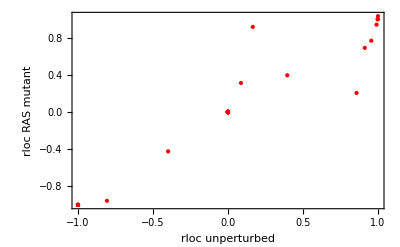

```mathematica
ListPlot[
Thread[{Flatten[rloc], Flatten[rlocRas]}],
PlotStyle->Directive[PointSize[Large],Red],
Frame->True,
FrameLabel->{"rloc unperturbed", "rloc RAS mutant" }
]
```

```mathematica
sRasDS = Dataset[
AssociationThread[
StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],
AssociationThread[StringReplace[ToString/@vars⟦3;;⟧, "Active"->  ""],#]&/@IdentityMatrix[Length[vars⟦3;;⟧]](si[sys, parsRAS, #]&/@vars⟦3;;⟧)
]
]
Export[
"results/orton-bmcsysbio-2009/stot-ras-true.tsv",
sRasDS]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

results/orton-bmcsysbio-2009/stot-ras-true.tsv

#### Simulate the RAS mutant population

```mathematica
popRas=Table[generateStochasticProteinAmounts[parsRAS, 0, .1],10000];
```

```mathematica
populationRas=Join[#,ss[sys,#]]&/@popRas//Quiet;
```

```mathematica
dfRas=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRas),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut.tsv",dfRas]
```

results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut.tsv

#### Simulate the RAS mutant population with Inhibitors

RAS Inhibition

```mathematica
parsRasRasi=perturbPar[parsRAS, reaction3Kcat, -.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasRasi])/(vars/.ss[sys, parsRAS])]]

popRasRasi=Table[generateStochasticProteinAmounts[parsRasRasi, 0, .1],2000];
populationRasRasi=Join[#,ss[sys,#]]&/@popRasRasi;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasRasi),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut-Rasi.tsv",df];
```

{boundEGFReceptor→3.20343×10^-16,freeEGFReceptor→3.20343×10^-16,SosActive→0.164598,RasActive→-0.24976,Raf1Active→-0.256892,MekActive→-0.234102,ErkActive→-0.221148,P90RskActive→-0.172756,PI3KActive→-0.000894664,AktActive→-0.00035355,C3GActive→3.20343×10^-16,Rap1Active→6.40685×10^-16,bRafActive→-0.223133}

Sos inhibition

```mathematica
parsRasSosi =perturbPar[parsRAS, reaction1Kcat, -.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasSosi])/(vars/.ss[sys, parsRAS])]]
popRasSosi=Table[generateStochasticProteinAmounts[parsRasSosi, 0, .1],2000];
populationRasSosi=Join[#,ss[sys,#]]&/@popRasSosi;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasSosi),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut-Sosi.tsv",df];
```

{boundEGFReceptor→3.20343×10^-16,freeEGFReceptor→3.20343×10^-16,SosActive→-0.250236,RasActive→-0.249556,Raf1Active→-0.256683,MekActive→-0.233915,ErkActive→-0.22097,P90RskActive→-0.172615,PI3KActive→-0.000893994,AktActive→-0.000353285,C3GActive→3.20343×10^-16,Rap1Active→3.20343×10^-16,bRafActive→-0.222956}

Raf1 inhibition

```mathematica
parsRasaf1i =perturbPar[parsRAS, reaction5Kcat, -.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasaf1i])/(vars/.ss[sys, parsRAS])]]
popRasRaf1i=Table[generateStochasticProteinAmounts[parsRasaf1i, 0, .1],2000];
populationRasRaf1i=Join[#,ss[sys,#]]&/@popRasRaf1i;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasRaf1i),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut-Raf1i.tsv",df];
```

{boundEGFReceptor→3.20343×10^-16,freeEGFReceptor→3.20343×10^-16,SosActive→0.0503526,RasActive→0.0502004,Raf1Active→-0.375108,MekActive→-0.0726226,ErkActive→-0.0683585,P90RskActive→-0.0527453,PI3KActive→0.000198393,AktActive→0.0000783808,C3GActive→3.20343×10^-16,Rap1Active→3.20343×10^-16,bRafActive→0.046189}

Mek inhibition

Mek is activated by both Raf1 (reaction 7) and bRaf (reaction 27),so we need to reduce both kcats.

```mathematica
parsRasMeki =perturbPar[parsRAS, {reaction7Kcat, reaction27kcat}, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasMeki])/(vars/.ss[sys, parsRAS])]]
popRasMeki=Table[generateStochasticProteinAmounts[parsRasMeki, 0, .1],2000];
populationRasMeki=Join[#,ss[sys,#]]&/@popRasMeki;
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasMeki),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut-Meki.tsv",df];
```

{boundEGFReceptor→3.20343×10^-16,freeEGFReceptor→3.20343×10^-16,SosActive→0.17457,RasActive→0.174018,Raf1Active→0.179757,MekActive→-0.247999,ErkActive→-0.234345,P90RskActive→-0.183254,PI3KActive→0.000716747,AktActive→0.000283137,C3GActive→0.,Rap1Active→0.,bRafActive→0.162056}

Erk inhibition

```mathematica
parsRasErki =perturbPar[parsRAS, reaction9Kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasErki])/(vars/.ss[sys, parsRAS])]]
popRasErki=Table[generateStochasticProteinAmounts[parsRasErki, 0, .1],2000];
populationRasErki=Join[#,ss[sys,#]]&/@popRasErki;
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasErki),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut-Erki.tsv",df];
```

{boundEGFReceptor→3.20343×10^-16,freeEGFReceptor→3.20343×10^-16,SosActive→0.174152,RasActive→0.173601,Raf1Active→0.179326,MekActive→0.167621,ErkActive→-0.233792,P90RskActive→-0.182814,PI3KActive→0.00071493,AktActive→0.00028242,C3GActive→3.20343×10^-16,Rap1Active→3.20343×10^-16,bRafActive→0.161661}

p90 inhibition

```mathematica
parsRasp90Rski =perturbPar[parsRAS, reaction11Kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasp90Rski])/(vars/.ss[sys, parsRAS])]]
popRasp90Rski=Table[generateStochasticProteinAmounts[parsRasp90Rski, 0, .1],2000];
populationRasp90Rski=Join[#,ss[sys,#]]&/@popRasp90Rski;
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasp90Rski),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut-p90Rski.tsv",df];
```

{boundEGFReceptor→3.20343×10^-16,freeEGFReceptor→3.20343×10^-16,SosActive→0.1851,RasActive→0.184512,Raf1Active→0.19062,MekActive→0.178292,ErkActive→0.16678,P90RskActive→-0.194344,PI3KActive→0.000762653,AktActive→0.000301269,C3GActive→0.,Rap1Active→3.20343×10^-16,bRafActive→0.172004}

PI3K inhibition

```mathematica
parsRasPI3Ki =perturbPar[parsRAS, {reaction13Kcat, reaction14Kcat}, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasPI3Ki])/(vars/.ss[sys, parsRAS])]]
popRasPI3Ki=Table[generateStochasticProteinAmounts[parsRasPI3Ki, 0, .1],2000];
populationRasPI3Ki=Join[#,ss[sys,#]]&/@popRasPI3Ki;
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasPI3Ki),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut-PI3Ki.tsv",df];
```

{boundEGFReceptor→3.20343×10^-16,freeEGFReceptor→3.20343×10^-16,SosActive→0.238131,RasActive→0.237359,Raf1Active→0.258762,MekActive→0.234455,ErkActive→0.218985,P90RskActive→0.164776,PI3KActive→-0.0772568,AktActive→-0.0310621,C3GActive→3.20343×10^-16,Rap1Active→6.40685×10^-16,bRafActive→0.22241}

Akt inhibition

```mathematica
parsRasAkti =perturbPar[parsRAS, reaction17Kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasAkti])/(vars/.ss[sys, parsRAS])]]
popRasAkti=Table[generateStochasticProteinAmounts[parsRasAkti, 0, .1],2000];
populationRasAkti=Join[#,ss[sys,#]]&/@popRasAkti;
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasAkti),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut-Akti.tsv",df];
```

{boundEGFReceptor→3.20343×10^-16,freeEGFReceptor→3.20343×10^-16,SosActive→-0.00972226,RasActive→-0.0096935,Raf1Active→0.0635499,MekActive→0.0141343,ErkActive→0.013277,P90RskActive→0.0101743,PI3KActive→-0.0000375565,AktActive→-0.179768,C3GActive→3.20343×10^-16,Rap1Active→6.40685×10^-16,bRafActive→-0.00886693}

C3G inhibition

```mathematica
parsRasC3Gi =perturbPar[parsRAS, reaction21kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasC3Gi])/(vars/.ss[sys, parsRAS])]]
popRasC3Gi=Table[generateStochasticProteinAmounts[parsRasC3Gi, 0, .1],2000];
populationRasC3Gi=Join[#,ss[sys,#]]&/@popRasC3Gi;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasC3Gi),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut-C3Gi.tsv",df];
```

{boundEGFReceptor→9.61028×10^-16,freeEGFReceptor→6.40685×10^-16,SosActive→0.0209512,RasActive→0.0208885,Raf1Active→0.021542,MekActive→-0.0303338,ErkActive→-0.0285244,P90RskActive→-0.0219362,PI3KActive→0.0000817535,AktActive→0.0000322998,C3GActive→-0.407262,Rap1Active→-0.407036,bRafActive→-0.054349}

Rap1 inhibition

```mathematica
parsRasRap1i =perturbPar[parsRAS, reaction23kcat, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasRap1i])/(vars/.ss[sys, parsRAS])]]
popRasRap1i=Table[generateStochasticProteinAmounts[parsRasRap1i, 0, .1],2000];
populationRasRap1i=Join[#,ss[sys,#]]&/@popRasRap1i;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasRap1i),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut-Rap1i.tsv",df];
```

{boundEGFReceptor→0.,freeEGFReceptor→0.,SosActive→0.0212972,RasActive→0.0212335,Raf1Active→0.0218979,MekActive→-0.0308333,ErkActive→-0.0289945,P90RskActive→-0.0222986,PI3KActive→0.0000831132,AktActive→0.000032837,C3GActive→0.,Rap1Active→-0.414807,bRafActive→-0.0552554}

Braf inhibition

```mathematica
parsRasbRafi =perturbPar[parsRAS, {reaction25kcat, reaction30kcat}, -0.25];
Thread[vars->Log2[(vars/.ss[sys, parsRasbRafi])/(vars/.ss[sys, parsRAS])]]
popRasbRafi=Table[generateStochasticProteinAmounts[parsRasbRafi, 0, .1],2000];
populationRasbRafi=Join[#,ss[sys,#]]&/@popRasbRafi;//Quiet
df=Dataset[
Prepend[
(Join[vars⟦3;;⟧,totalProteins]/.populationRasbRafi),
Join[vars⟦3;;⟧,totalProteins]
]
];
Export["results/orton-bmcsysbio-2009/simulations/steady-state-sigma=0.1-RASmut-bRafi.tsv",df];
```

{boundEGFReceptor→3.20343×10^-16,freeEGFReceptor→3.20343×10^-16,SosActive→0.126044,RasActive→0.125652,Raf1Active→0.129727,MekActive→-0.180086,ErkActive→-0.169922,P90RskActive→-0.132202,PI3KActive→0.00050922,AktActive→0.000201167,C3GActive→3.20343×10^-16,Rap1Active→3.20343×10^-16,bRafActive→-0.345093}